ϕ_0=-53.0623°    θ_0=-0.621724°    θ_∞=-112.171°    α=-164.611°

Ε=0.244229    L=-3.51127    ϵ=2.64994    k=12.329    a=2.04726    b=5.024    c=5.42512    W0=0.010439    argInf=-1.

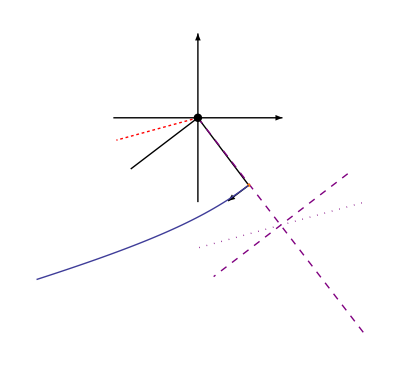

```mathematica
Clear["Global`*"];    x0=2.03;    y0=-2.70;    vx0=-0.8259;    vy0=-0.6312;    Z=1;
Ε=-Z/Sqrt[x0^2+y0^2]+(vx0^2+vy0^2)/2;    L=x0 vy0-y0 vx0;    ϵ=Sqrt[1+2Ε L^2/Z^2];    r0=Sqrt[x0^2+y0^2];    ϕ0=ArcTan[x0,y0];    
If[Ε≤0,{Print["Ε<=0"],Interrupt[]},{}];    k=L^2/Z;    a=k/(ϵ^2-1);     b=a Sqrt[ϵ^2-1];    c=ϵ a;
θinf=Piecewise[{{ArcCos[-1/ϵ],L≥0},{-ArcCos[-1/ϵ],L<0}}];
Subscript[θ, 0]=ArcCos[(L^2/(Z r0)-1)/ϵ];    Angle[x1_,y1_,x2_,y2_]:=ArcCos[(x1 x2+y1 y2)/Sqrt[(x1^2+y1^2)(x2^2+y2^2)]];
θ0=Piecewise[{{Subscript[θ, 0],(L≥0∧Angle[x0,y0,vx0,vy0]≤π/2)∨(L<0∧Angle[x0,y0,vx0,vy0]>π/2)},{-Subscript[θ, 0],(L<0∧Angle[x0,y0,vx0,vy0]≤π/2)∨(L≥0∧Angle[x0,y0,vx0,vy0]>π/2)}}];
α=ϕ0+θinf-θ0;   W0=-(2L/Sqrt[ϵ^2-1])ArcTanh[Sqrt[(ϵ-1)/(ϵ+1)]Tan[θ0/2]];  argInf=Sqrt[(ϵ-1)/(ϵ+1)]Tan[θinf/2];
Riffle[{"ϕ_0=",180ϕ0/π,  "θ_0=", 180θ0/π, "θ_∞=",180θinf/π,  "α=",180α/π, ""},"°    ",3]//Row//Print
Riffle[{"Ε=",Ε,"L=",L,"ϵ=",ϵ,"k=",k,"a=",a, "b=",b,"c=",c,"W0=",W0,"argInf=",argInf},"    ",3]//Row//Print

r[t_]:={x[t],y[t]}; newton=Thread[r''[t]==-Z r[t]/(r[t].r[t])^(3/2)]; bc1=Thread[r[0]=={x0,y0}];  bc2=Thread[Evaluate[r'[0]=={vx0,vy0}]];
motion=Join[newton,bc1,bc2]; traj=r[t]/.NDSolve[motion,r[t],{t,0,10}];  plot=ParametricPlot[{traj⟦1,1⟧/r0,traj⟦1,2⟧/r0},{t,0,10}];
Ox=c Cos[ϕ0-θ0]/r0; Oy=c Sin[ϕ0-θ0]/r0; 
Show[{Graphics[{
Arrow[{{-1,0},{1,0}}],Arrow[{{0,-1},{0,1}}],(* the coordinate axis *)
Arrow[{{0,0},{x0/r0,y0/r0},{(x0+vx0)/r0,(y0+vy0)/r0}}], (* initial position and velocity vector *)
{Black,Line[{{0,0},{vx0/Sqrt[vx0^2+vy0^2],vy0/Sqrt[vx0^2+vy0^2]}}]},(* initial velocity direction *)
{Red,Dashing[Tiny],Line[{{0,0},{Cos[α],Sin[α]}}]}, (* asymptotic velecity direction *)
{Purple,Dotted,Line[{{Ox+Cos[α],Oy+Sin[α]},{Ox-Cos[α],Oy-Sin[α]}}]}, (* asymptote *)
{Purple,Dashed,Line[{{0,0},{2Ox,2Oy}}]}, 
{Purple,Dashed,Line[{{Ox+1/Sqrt[1+(Ox/Oy)^2], Oy-Ox/(Oy Sqrt[1+(Ox/Oy)^2])},{Ox-1/Sqrt[1+(Ox/Oy)^2], Oy+Ox/(Oy Sqrt[1+(Ox/Oy)^2])}}]},(* axis for the polar coordinate *)
{Black,Disk[{0,0},0.05]}, (* nuclei *)
{Orange,Disk[{x0/r0,y0/r0},0.02]}  (* electron *)
}],plot}]
```